```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
kappa:=0.548008;
chip := 1.79285;
chin:=-1.913;
gp:=0.27;
gn:=0.38;
r:= 2.08;
Mp:=0.93828;
Mn:=0.93957;
mpi=0.13957;
gmn[0]:=0.149;
gmn[1]:=0.40;
gmn[2]:=1.5;
gmn[3]:=0.85;
gmn[4]:=0.60;

M2[n_]:=4*kappa^2(n+1/2);
(*beta[q_,m1_,m2_]:=√(1+((m1^2-m2^2)^2)/q^4-2(m1^2+m2^2)/q^2);*)
```

```mathematica
(*gamma[n_,q_,m1_ ,m2_,L_]:=gmn[n] q/(√M2[n])(HeavisideTheta[q^2-4 mpi^2]*(beta[q,m1,m2]/beta[√M2[n],m1,m2])^(2L+1));*)
gamma[n_,q_]:=gmn[n](√(M2[n]/q^2))^2((q^2-4 mpi^2)/(M2[n]-4 mpi^2))^1.5
```

```mathematica
d[q_,n_]:=M2[n]-q^2-I*q*gamma[n,q];
```

```mathematica
F1p[q_]:=(M2[0]M2[1])/(d[q,0]d[q,1]);
```

```mathematica
F2p[q_]:=chip*((1-gp)(M2[0]M2[1]M2[2])/(d[q,0]d[q,1]d[q,2])+gp*(M2[0]M2[1]M2[2]M2[3]M2[4])/(d[q,0]d[q,1]d[q,2]d[q,3]d[q,4]));
```

```mathematica
GMp[q_]:=F1p[q]+F2p[q];
```

```mathematica
GEp[q_]:=F1p[q]+q^2/(4*Mp^2)F2p[q];
```

```mathematica
Geff[q_]:=√((q^2/(2 Mp^2)(Abs[GMp[q]])^2+(Abs[GEp[q]])^2)/(1+q^2/(2 Mp^2)));
```

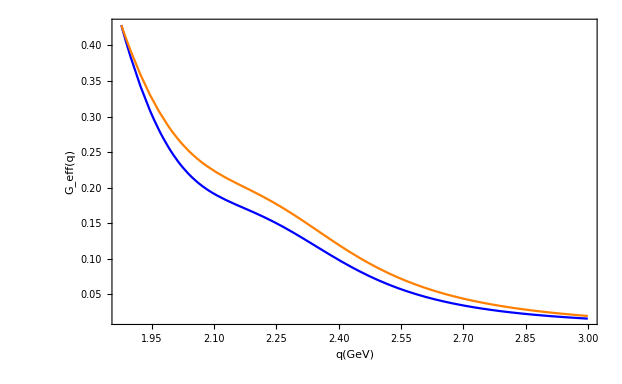

```mathematica
Plot[{Geff[q],Abs[GEp[q]]},{q,2Mp,3},PlotRange->All,Frame->True,FrameStyle->Directive[Black,20],Axes->False,LabelStyle->Directive[Blue],BaseStyle->{Large,FontFamily->"Courier",FontSize->12},PlotStyle-> {Blue,Orange},FrameLabel->{"q(GeV)","G_eff(q)"}]
```

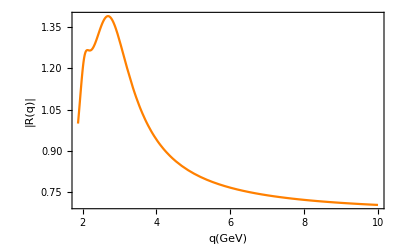

```mathematica
Plot[{Abs[GEp[q]]/Abs[GMp[q]]},{q,2Mp,10},PlotRange->All,Frame->True,FrameStyle->Directive[Black,20],Axes->False,LabelStyle->Directive[Blue],BaseStyle->{Large,FontFamily->"Courier",FontSize->12},PlotStyle-> {Blue,Orange},FrameLabel->{"q(GeV)","|R(q)|"}]
```

```mathematica
Rat[q_]:=Abs[GEp[q]]/Abs[GMp[q]];
Export["/Users/hunululu/Projects/TLFF/tlgpeff/TL40x.txt",Table[Abs[Geff[q]],{q,0.01,10,0.01}]]
Export["/Users/hunululu/Projects/TLFF/tlgpeff/R40x.txt",Table[Rat[q],{q,0.01,10,0.01}]]
```

/Users/hunululu/Projects/TLFF/tlgpeff/TL40x.txt

/Users/hunululu/Projects/TLFF/tlgpeff/R40x.txt

```mathematica
F1n[q_]:=-r/3((M2[0]M2[1])/(d[q,0]d[q,1])-(M2[0]M2[1]M2[2])/(d[q,0]d[q,1]d[q,2]));
F2n[q_]:=chin((1-gn)(M2[0]M2[1]M2[2])/(d[q,0]d[q,1]d[q,2])+gn (M2[0]M2[1]M2[2]M2[3]M2[4])/(d[q,0]d[q,1]d[q,2]d[q,3]d[q,4]));
GMn[q_]:=F1n[q]+F2n[q];
GEn[q_]:=F1n[q]+q^2/(4 Mn^2) F2n[q];
```

```mathematica
Geffn[q_]:=√((q^2/(2 Mn^2)(Abs[GMn[q]])^2+(Abs[GEn[q]])^2)/(1+q^2/(2 Mn^2)));
```

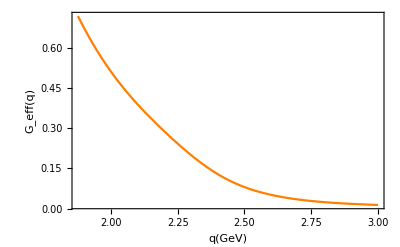

```mathematica
Plot[{Geffn[q]},{q,2Mp,3},PlotRange->All,Frame->True,FrameStyle->Directive[Black,20],Axes->False,LabelStyle->Directive[Blue],BaseStyle->{Large,FontFamily->"Courier",FontSize->12},PlotStyle-> {Blue,Orange},FrameLabel->{"q(GeV)","G_eff(q)"}]
```

```mathematica
Export["/Users/hunululu/Projects/TLFF/tlgpeff/TLNeu.txt",Table[Geffn[q],{q,0.01,10,0.01}]]
Export["/Users/hunululu/Projects/TLFF/tlgpeff/QNeu.txt",Table[q,{q,0.01,10,0.01}]]
```

/Users/hunululu/Projects/TLFF/tlgpeff/TLNeu.txt

/Users/hunululu/Projects/TLFF/tlgpeff/QNeu.txt

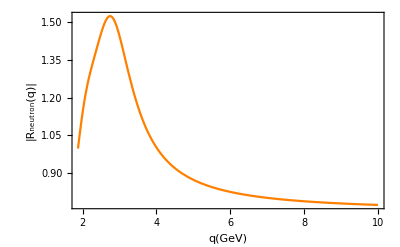

```mathematica
Plot[{Abs[GEn[q]]/Abs[GMn[q]]},{q,2Mp,10},PlotRange->All,Frame->True,FrameStyle->Directive[Black,20],Axes->False,LabelStyle->Directive[Blue],BaseStyle->{Large,FontFamily->"Courier",FontSize->12},PlotStyle-> {Blue,Orange},FrameLabel->{"q(GeV)","|R_neutron(q)|"}]
```